# P05. Интерполирование по системе оптимальных узлов

Захаренко Евгений
КМ, 3 курс, 
Вариант 3

## Задание 1.

### 1. Пусть функция f(x)∈MC^(n+1)[-1;1] задана на отрезке [-1;1] аналитически. Построить интерполяционный многочлен P_n(x)≈f(x) указанной степени n с минимальной верхней гранью погрешности по оптимальным узлам x_k=cos(π (2k+1))/(2 (n+1)), k=OverBar[0,n].

```mathematica
f[x_]:=3^x;
n=4;
```

```mathematica
X=Table[Cos[(π(2 k+1))/(2(n+1)) ],{k,0,n}]//N
```

{0.951057,0.587785,0.,-0.587785,-0.951057}

```mathematica
IPol=InterpolatingPolynomial[Table[{X⟦i⟧,f[X⟦i⟧]},{i,1,Length[X]}],x]//Simplify//Expand
```

1.+1.09429 x+0.602691 x^2+0.238152 x^3+0.0638159 x^4

### 2. Оценить погрешность интерполирования |R_n(f,·)|≤M/((n+1)! 2^n): , где M=max_(-1≤x≤1) |f^(n+1)(x)|.

```mathematica
V=Maximize[{D[f[x],{x,n+1}],-1≤ x≤ 1},x]⟦1⟧//N
Z=Minimize[{D[f[x],{x,n+1}],-1≤ x≤ 1},x]⟦1⟧//N
M=Max[Abs[V],Abs[Z]]
```

4.80113

0.533459

4.80113

```mathematica
M/((n+1)! 2^n)//N
```

0.00250059

### 3. Изобразить исходную функцию, узлы и полученный интерполяционный многочлен в одной системе координат.

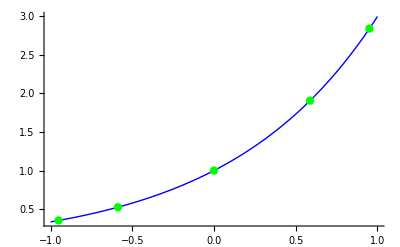

```mathematica
Show[Plot[f[x],{x,-1,1},PlotStyle->{Blue,Thick}],Plot[IntPol,{x,-1,1},PlotStyle->Red],Graphics[{Green,PointSize-> 0.015,Point[Table[{X⟦i⟧,f[X⟦i⟧]},{i,1,n+1}]]}]]
```

## Задание 2.

### 1. Пусть функция f(x)∈MC^(n+1)[a;b] задана на отрезке [a;b] аналитически. Построить интерполяционный многочлен P_n(x)≈f(x) с минимальной верхней гранью погрешности, не превышающей ϵ. Число необходимых n+1 по оптимальных узлов x_k=(b-a)/2 cos(π (2k+1))/(2 (n+1))+(a+b)/2, k=OverBar[0,n], определить из условия оценки верхней грани погрешности (M (b-a)^(n+1))/((n+1)! 2^(2n+1))≤ϵ, где M=max_(a≤x≤b) |f^(n+1)(x)|.

```mathematica
ClearAll[f,X,M,k]
```

```mathematica
f[x_]:=Sin[3x];
a=1; b=3; ϵ=10^-7;
n=1;
```

```mathematica
While[(Maximize[{Abs[D[f[x],{x,n+1}]],a≤ x≤ b},x]⟦1⟧(b-a)^(n+1))/((n+1)! 2^(2n+1))   > ϵ,n++];
n
```

12

```mathematica
X=Table[(b-a)/2 Cos[(π(2 k+1))/(2(n+1))]+(a+b)/2,{k,0,n}]//N;
```

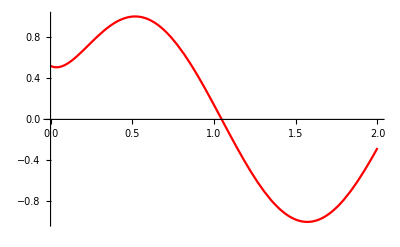

```mathematica
(*интерполяционный многочлен*)
IPol2=InterpolatingPolynomial[Table[{X⟦i⟧,f[X⟦i⟧]},{i,1,Length[X]}],x]//Simplify//Expand;
Plot[IPol2,{x,0,2},PlotStyle->Red]
```

### 2. Изобразить исходную функцию, узлы и полученный интерполяционный многочлен в одной системе координат.

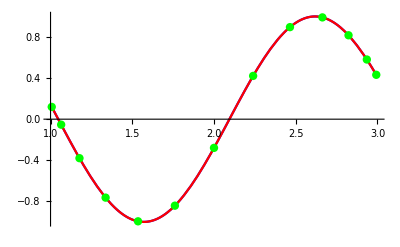

```mathematica
Show[Plot[f[x],{x,1,3},PlotStyle->Blue],Plot[IPol2,{x,1,3},PlotStyle->Red],Graphics[{Green,PointSize-> 0.015,Point[Table[{X⟦i⟧,f[X⟦i⟧]},{i,1,n+1}]]}]]
```

## Задание 3.

### Решить предложенную задачу теории погрешности интерполирования фиксированными узлами, применяя неравенство |R_n(f,y)|≤M/((n+1)!)|ω_n(y)| в случае фиксированной точки интерполирования y либо неравенство вида |R_n(f,·)|≤M/((n+1)!)max_(a≤x≤b)|ω_n(x)| для погрешности на всём отрезке интерполирования (M=max_(a≤x≤b) |f^(n+1)(x)|): Оценить погрешность интерполирования функции f(x)=arccos(x) на отрезке [0; 1] многочленом Лагранжа пятой степени на равномерной сетке.

```mathematica
ClearAll[a,b,n,f,M,ω]
f[x_]:=Sin[x]
a=0;b=π/4; 
n=5;
h=0.01;
```

```mathematica
M=Maximize[{Abs[f''''''[x]],a≤ x≤ b},x]//N
```

{0.707107,{x→0.785398}}

T.к. М неограничена, то погрешность считается по 2 формуле и равна ∞.

## Задание 4.

### Решить предложенную задачу теории погрешности интерполирования по оптимальным узлам, применяя неравенство |R_n(f,·)|≤(M (b-a)^(n+1))/((n+1)! 2^(2n+1)), где M=max_(a≤x≤b) |f^(n+1)(x)|: Определить степень интерполяционного многочлена Лагранжа, обеспечивающую точность приближения функции sin(x) на отрезке [0;π/2] не хуже 10^-2.

```mathematica
ClearAll[f,X,M,a,b,n]
```

```mathematica
f[x_]:=Cos[x];
a=π/2;b=3π/4;
ϵ=10^-2;
n=1;
```

```mathematica
M=Maximize[{Abs[D[f[x],{x,n+1}]],a≤ x≤ b},x]//N
```

{1.,{x→1.5708}}

```mathematica
While[(M⟦1⟧(b-a)^(n+1))/((n+1)! 2^(2n+1))   ≥ ϵ,n++];
n
```

3

```mathematica
(M⟦1⟧(b-a)^(n+1))/((n+1)! 2^(2n+1))//N
```

0.00198179

## Attention!

### Линейная интерполяция

линейная интерполяция → степень равна 1 (n=1)
x_0,x_0+h ∈[a,b]

|R_1|≤M/2 max_(x_0≤x≤x_0+h)|ω_1(x)|

M=max_(a≤x≤b) |f''(x)|

w_1(x)=(x-x_0)(x-x_0-h)
w_1(x)=x-x_0+x-x_0-h=0

### Квадратичная интерполяция